### Start choosing the example:

```mathematica
t=25;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t];
MFGEquations=DataToEquations[Data];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

Good job!

DataToEquations: Done.

{0.023413,Null}

```mathematica
v0=MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j587→0,j588→2-1,j589→1,j590→1,j591→2,j592→2-1,j593→0,j594→0,j595→0,j596→0,jt597→2-1,jt598→0,jt599→0,jt600→0,jt601→0,jt602→0,jt603→2-1,jt604→1,jt605→1,jt606→0,u607→5,u608→5,u609→6,u610→5,u611→6,u612→2-1+5,u613→5,u614→-1+6,u615→5,u616→6|>

#### Non-linear case

```mathematica
alpha = 1.9;
beta = 0;
A = 0.2;
Parameters["alpha"] = alpha;
Parameters
```

<|alpha→1.9,beta→0,g[m]→Log,W[x,A]→Function[{x,a},a Sin[2 π (x+1/4)]^2],V[x]→Function[{x$},W$119513[x$,A]],H[x,p,m]→Function[{x$,p$,m$},p$^2/(2 m$^alpha)+V$119513[x$]-g$119513[m$]]|>

```mathematica
nsol1=FixedPoint[FixedSolverStepX1[MFGEquations], MFGEquations["criticalreduced1"][[2]]//N,3, SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<10^(-17)&)]//KeySort
```

<|j587→0.,j588→1.,j589→1.,j590→1.,j591→2.,j592→1.,j593→0.,j594→0.,j595→0.,j596→0.,jt597→1.,jt598→0.,jt599→0.,jt600→0.,jt601→0.,jt602→0.,jt603→1.,jt604→1.,jt605→1.,jt606→0.,u607→5.,u608→5.,u609→6.6767,u610→5.,u611→6.6767,u612→6.,u613→5.,u614→5.,u615→5.,u616→6.|>

```mathematica
(Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]])/.nsol1
(Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]])/.nsol2
(Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]])/.nsol3n
```

0.676702

4.53914×10^-13

4.53914×10^-13

```mathematica
nsol2=FixedPoint[FixedSolverStepX2[MFGEquations], MFGEquations["criticalreduced1"][[2]],10, SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<10^(-17)&)]//KeySort
```

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j587-j592-u607+u612==0.676702&&j589-j594-u609+u614==-0.676702

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j587-j592-u607+u612==0.676702&&j589-j594-u609+u614==-0.676702

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j587-j592-u607+u612==0.676702&&j589-j594-u609+u614==-0.676702

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j587-j592-u607+u612==0.676702&&j589-j594-u609+u614==-0.676702

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j587-j592-u607+u612==0.676702&&j589-j594-u609+u614==-0.676702

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j587-j592-u607+u612==0.676702&&j589-j594-u609+u614==-0.676702

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j587-j592-u607+u612==0.676702&&j589-j594-u609+u614==-0.676702

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j587-j592-u607+u612==0.676702&&j589-j594-u609+u614==-0.676702

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j587-j592-u607+u612==0.676702&&j589-j594-u609+u614==-0.676702

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j587-j592-u607+u612==0.676702&&j589-j594-u609+u614==-0.676702

<|j587→0.,j588→2.-1. 1.,j589→1.,j590→0.+1. 1.,j591→2.,j592→2.-1. 1.,j593→0.,j594→0.,j595→0.,j596→0.,jt597→2.-1. 1.,jt598→0.,jt599→0.,jt600→0.,jt601→0.,jt602→0.,jt603→2.-1. 1.,jt604→0.+1. 1.,jt605→0.+1. 1.,jt606→0.,u607→5.,u608→5,u609→6.6767,u610→5,u611→6.6767,u612→2.6767-1. 1.+1. 5.,u613→5,u614→-0.676702-1. 1.+1. 6.6767,u615→5,u616→6.6767|>

```mathematica
nsol3n=FixedPoint[FixedSolverStepX3[MFGEquations], MFGEquations["criticalreduced1"][[2]],10, SameTest->(Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<10^(-17)&)]//KeySort
```

FixedX3: next step: j587-j592-u607+u612==0.676702&&j589-j594-u609+u614==-0.676702

FixedX3: next step: j587-j592-u607+u612==0.676702&&j589-j594-u609+u614==-0.676702

FixedX3: next step: j587-j592-u607+u612==0.676702&&j589-j594-u609+u614==-0.676702

«7 more identical outputs»

<|j587→0.,j588→2.-1. 1.,j589→1.,j590→0.+1. 1.,j591→2.,j592→2.-1. 1.,j593→0.,j594→0.,j595→0.,j596→0.,jt597→2.-1. 1.,jt598→0.,jt599→0.,jt600→0.,jt601→0.,jt602→0.,jt603→2.-1. 1.,jt604→0.+1. 1.,jt605→0.+1. 1.,jt606→0.,u607→5.,u608→5,u609→6.6767,u610→5,u611→6.6767,u612→2.6767-1. 1.+1. 5.,u613→5,u614→-0.676702-1. 1.+1. 6.6767,u615→5,u616→6.6767|>

```mathematica
Norm[(MFGEquations["Nrhs"]-MFGEquations["Nlhs"])/.nsol3n]
```

3.14018×10^-16

### What is this plot for?

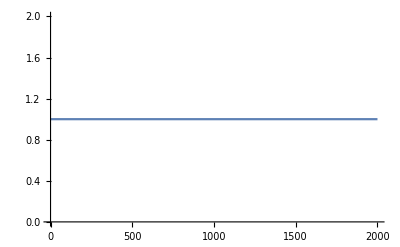
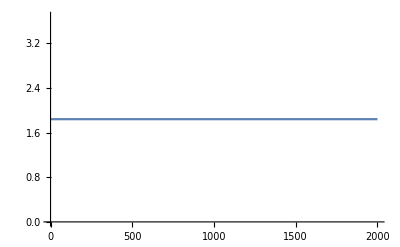
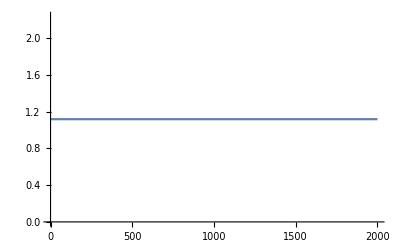
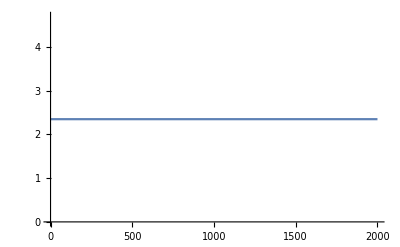
<|{2,1->2}→-Graphics-,{ex746,1->ex746}→-Graphics-,{3,2->3}→-Graphics-,{ex747,3->ex747}→-Graphics-,{2,en745->2}→-Graphics-,{1,1->2}→-Graphics-,{1,1->ex746}→-Graphics-,{2,2->3}→-Graphics-,{3,3->ex747}→-Graphics-,{en745,en745->2}→-Graphics-|>

```mathematica
Function[a,ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-a/(m^(1-alpha)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]]/@jv
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will always retrieve the most up - to - date values.

```mathematica
f=<|c->b|>
```

<|c→b|>

```mathematica
AssociateTo[f,v->m]
```

<|c→b,v→m|>

```mathematica
f
```

<|c→b,v→m|>

```mathematica
f
```

<|c→b,v→m|>

```mathematica
Append[f,m->b]
```

<|c→b,v→m,m→b|>

```mathematica
f
```

<|c→b,v→m|>

```mathematica
AssociateTo[f,m->b]
```

<|c→b,v→m,m→b|>

```mathematica
f
```

<|c→b,v→m,m→b|>

```mathematica
f=Append[f,g->k]
```

<|c→b,v→m,m→b,g→k|>

```mathematica
f
```

<|c→b,v→m,m→b,g→k|>

```mathematica
Reduce[j589==0.+1. j589&&j589==0.+1. j589]
```

True

```mathematica
Solve[x^3 ==1, Reals]
```

{{x→1}}

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

$Aborted